## MRAC for unknown overall gain (Figure 10.2)

System structure = underdamped oscillator, with G_0(s) = 1/(s^2+s+1)
used for book, Adaptive Control chapter

```mathematica
Clear["Global`*"];
```

stable for small learning rate and small step size in the command signal

```mathematica
adapt[γ_,a_]:=Module[{e,t,k,km,eqs,y,ym,θ,u,init,pars},
tend=100;
e[t]=y[t]-ym[t];
uc[t_]:=a Sign[Sin[2π t/40]];
eqs={
y''[t]+y'[t]+y[t]==k u[t], 
ym''[t]+ym'[t]+ym[t]==km uc[t],
θ'[t]==-γ ym[t]e[t],
u[t]== θ[t]uc[t]};
init={y[0]==0,y'[0]==0,ym[0]==0,ym'[0]==0,θ[0]==0};pars={k->1,km->1};

NDSolveValue[{eqs/.pars,init},
{y,ym,θ,u},{t,0,tend},MaxSteps->10^5]//Quiet]
```

unstable for larger learning rate

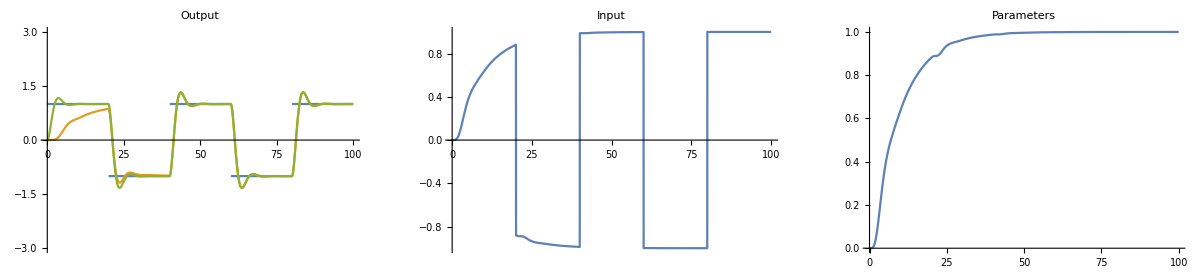

```mathematica
{ys,yms,θs,us}=adapt[0.1,1];
p1=Plot[{uc[t],ys[t],yms[t]},{t,0,tend},PlotRange->{-3,3},PlotLabel->"Output"];
p2=Plot[us[t],{t,0,tend},PlotRange->All,PlotLabel->"Input"]; 
p3=Plot[θs[t],{t,0,tend},PlotRange->All,PlotLabel->"Parameters"];

GraphicsRow[{p1,p2,p3},ImageSize->Full]
```

unstable for larger step size

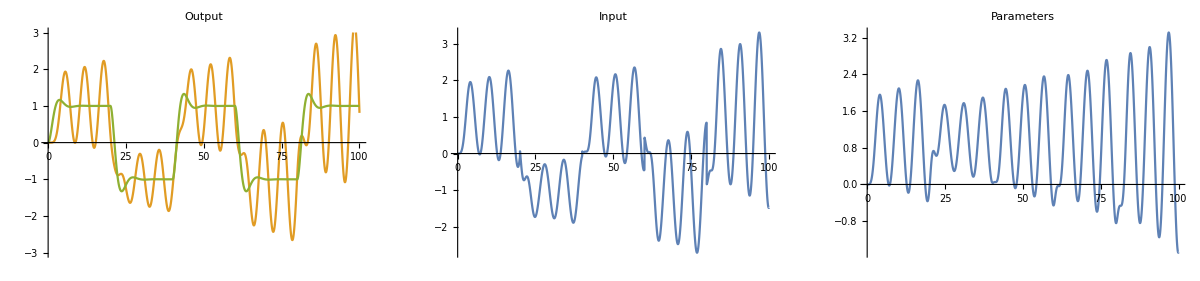

```mathematica
{ys1,yms1,θs1,us1}=adapt[1.1,1];
p4=Plot[{uc1[t],ys1[t],yms1[t]},{t,0,tend},PlotRange->{-3,3},PlotLabel->"Output"];
p5=Plot[us1[t],{t,0,tend},PlotRange->All,PlotLabel->"Input"]; 
p6=Plot[θs1[t],{t,0,tend},PlotRange->All,PlotLabel->"Parameters"];

GraphicsRow[{p4,p5,p6},ImageSize->Full]
```

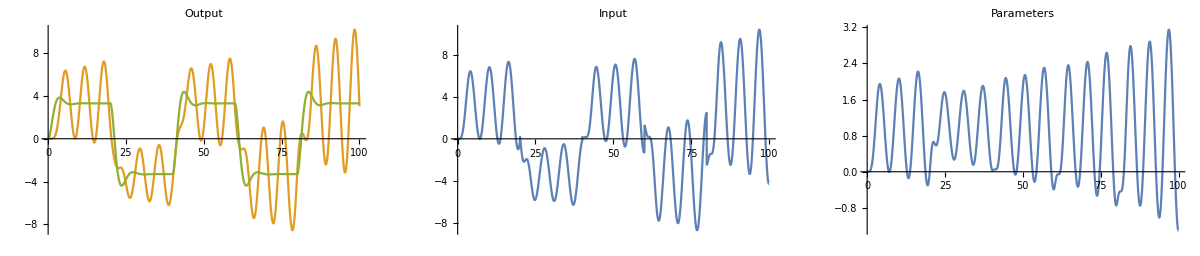

```mathematica
{ys2,yms2,θs2,us2}=adapt[0.1,3.3];
p7=Plot[{uc2[t],ys2[t],yms2[t]},{t,0,tend},PlotRange->All,PlotLabel->"Output"];
p8=Plot[us2[t],{t,0,tend},PlotRange->All,PlotLabel->"Input"]; 
p9=Plot[θs2[t],{t,0,tend},PlotRange->All,PlotLabel->"Parameters"];

GraphicsRow[{p7,p8,p9},ImageSize->Full]
```

Export data

```mathematica
dt=0.1;
dat=Table[Through[{ys,yms,θs,us,ys2,yms2,θs2,us2}[t]],{t,0,tend,dt}];(* 
SetDirectory[NotebookDirectory[]];
Export["mrac2ndOrder.dat",dat]; 
*)
```